## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBA1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_FBA1_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; _fdp,g3p,dhap

Structure: 10-Aug

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.000102656 | 0.0000975232
0.000107789 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00002 | 0.000019
0.000021 |  | M | 7.5 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10};
kmPriorities = {1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; _fdp,g3p,dhap

Structure: 10-Aug

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | fdp | Null | 0.000102656 | 0.0000975232
0.000107789 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00002 | 0.000019
0.000021 |  | M | 7.5 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[fdp^c⇌dhap^c+g3p^c, FBA1]
```

```mathematica
catalyticBranch={"E_FBA1[c] + fdp[c] <=> E_FBA1[c]&fdp",

				"E_FBA1[c]&fdp <=> E_FBA1[c]&dhap&g3p",
				
				"E_FBA1[c]&dhap&g3p<=> E_FBA1[c]&dhap + g3p[c]",
				"E_FBA1[c]&dhap <=> E_FBA1[c] + dhap[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA11,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA12,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA13,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA14}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA11,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA12],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA13,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA14]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((FBA1^c&fdp^c)_^-((FBA1^c&dhap^c&g3p^c)_^)/K_FBA13) Volume_c k_FBA13^⟶}

Volume_c (-(FBA1^c&dhap^c&g3p^c)_^ k_FBA13^⟵+(FBA1^c&fdp^c)_^ k_FBA13^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur = 0.000102656;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
```

k_FBA11^⟵

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_FBA11^⟵→(9741.27 k_FBA11^⟶ k_FBA12^⟶ k_FBA13^⟶ k_FBA14^⟶)/(k_FBA12^⟵ k_FBA13^⟵ k_FBA14^⟵)

```mathematica
flux = 0.0006081074005408912;
FluxExpression = absoluteFlux /. {metabolite["fdp", "c"] -> 0.0010306264592820896,metabolite["g3p","c"]-> 0.0001,
metabolite["dhap","c"]-> 0.0001,
     parameter["FBA1_total"] -> 0.0000475600739639428, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "FBA1"] /. FluxExpression/.haldaneSub[[1,1]];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
1	0	2.0000000000000003e-6	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909091
1	0	3.1697863849222286e-6	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.13680688860321005
1	0	5.023772863019165e-6	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310186
1	0	7.96214341106994e-6	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.000012619146889603861	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.3868631798468569
1	0	0.00002	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.49999999999999994
1	0	0.00003169786384922229	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.00005023772863019165	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.00007962143411069939	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868981
1	0	0.0001261914688960386	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.00020000000000000004	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	2.0000000000000003e-6	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909091
1	0	3.1697863849222286e-6	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.13680688860321005
1	0	5.023772863019165e-6	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310186
1	0	7.96214341106994e-6	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.000012619146889603861	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.3868631798468569
1	0	0.00002	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.49999999999999994
1	0	0.00003169786384922229	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.00005023772863019165	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.00007962143411069939	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868981
1	0	0.0001261914688960386	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.00020000000000000004	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	7.000000000000002e-6	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.000011094252347227801	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.13680688860321008
1	0	0.00001758320502056708	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.000027867501938744792	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.000044167014113613516	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.3868631798468569
1	0	0.00007000000000000002	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0001758320502056708	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491989
1	0	0.0002786750193874482	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868984
1	0	0.0004416701411361352	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0007000000000000001	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	0.41211435266581287
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt"	6.020288008989064
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateRev_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateFor_fdp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateRev_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA1_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 26.0756263952
best_fit: 25.4129707403
best_fit: 24.8144411241
best_fit: 26.1353843145
best_fit: 26.0608441143
best_fit: 25.0046933526
best_fit: 32.8657872523
best_fit: 32.759060792
best_fit: 24.7724340051
best_fit: 24.8300500524

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
10 | haldaneRatio_1 | 0.000321211 | 1.03177×10^-7 | 7.58979×10^-8 | 0.0739342 | 0.000102656 | 0.00010258
1 | relRateFor_fdp | 0.0771162 | 0.00594691 | 0.0147904 | 16.2695 | 0.0909091 | 0.0761186
1 | relRateFor_fdp | 0.0735337 | 0.00540721 | 0.021309 | 15.5759 | 0.136807 | 0.115498
1 | relRateFor_fdp | 0.0684921 | 0.00469117 | 0.0292912 | 14.5902 | 0.20076 | 0.171469
1 | relRateFor_fdp | 0.061781 | 0.0038169 | 0.0377577 | 13.2601 | 0.284747 | 0.24699
1 | relRateFor_fdp | 0.0534791 | 0.00286002 | 0.0448221 | 11.586 | 0.386863 | 0.342041
1 | relRateFor_fdp | 0.044092 | 0.00194411 | 0.048271 | 9.6542 | 0.5 | 0.451729
1 | relRateFor_fdp | 0.0344976 | 0.00119008 | 0.0468195 | 7.63606 | 0.613137 | 0.566317
1 | relRateFor_fdp | 0.0256518 | 0.000658017 | 0.0410233 | 5.7355 | 0.715253 | 0.674229
1 | relRateFor_fdp | 0.018239 | 0.000332662 | 0.0328705 | 4.11272 | 0.79924 | 0.766369
1 | relRateFor_fdp | 0.0125083 | 0.000156458 | 0.0245067 | 2.83907 | 0.863193 | 0.838686
1 | relRateFor_fdp | 0.00834843 | 0.0000696963 | 0.0173085 | 1.90394 | 0.909091 | 0.891782
1 | relRateFor_fdp | 0.0771162 | 0.00594691 | 0.0147904 | 16.2695 | 0.0909091 | 0.0761186
1 | relRateFor_fdp | 0.0735337 | 0.00540721 | 0.021309 | 15.5759 | 0.136807 | 0.115498
1 | relRateFor_fdp | 0.0684921 | 0.00469117 | 0.0292912 | 14.5902 | 0.20076 | 0.171469
1 | relRateFor_fdp | 0.061781 | 0.0038169 | 0.0377577 | 13.2601 | 0.284747 | 0.24699
1 | relRateFor_fdp | 0.0534791 | 0.00286002 | 0.0448221 | 11.586 | 0.386863 | 0.342041
1 | relRateFor_fdp | 0.044092 | 0.00194411 | 0.048271 | 9.6542 | 0.5 | 0.451729
1 | relRateFor_fdp | 0.0344976 | 0.00119008 | 0.0468195 | 7.63606 | 0.613137 | 0.566317
1 | relRateFor_fdp | 0.0256518 | 0.000658017 | 0.0410233 | 5.7355 | 0.715253 | 0.674229
1 | relRateFor_fdp | 0.018239 | 0.000332662 | 0.0328705 | 4.11272 | 0.79924 | 0.766369
1 | relRateFor_fdp | 0.0125083 | 0.000156458 | 0.0245067 | 2.83907 | 0.863193 | 0.838686
1 | relRateFor_fdp | 0.00834843 | 0.0000696963 | 0.0173085 | 1.90394 | 0.909091 | 0.891782
1 | relRateFor_fdp | 0.391298 | 0.153114 | 0.132914 | 146.206 | 0.0909091 | 0.223823
1 | relRateFor_fdp | 0.36037 | 0.129866 | 0.176867 | 129.282 | 0.136807 | 0.313673
1 | relRateFor_fdp | 0.320647 | 0.102814 | 0.219312 | 109.241 | 0.20076 | 0.420072
1 | relRateFor_fdp | 0.273454 | 0.074777 | 0.24971 | 87.6955 | 0.284747 | 0.534458
1 | relRateFor_fdp | 0.222226 | 0.0493843 | 0.258469 | 66.8114 | 0.386863 | 0.645332
1 | relRateFor_fdp | 0.17174 | 0.0294947 | 0.242523 | 48.5047 | 0.5 | 0.742523
1 | relRateFor_fdp | 0.126517 | 0.0160065 | 0.207355 | 33.8187 | 0.613137 | 0.820492
1 | relRateFor_fdp | 0.0893858 | 0.00798982 | 0.163457 | 22.853 | 0.715253 | 0.878709
1 | relRateFor_fdp | 0.0610598 | 0.0037283 | 0.120652 | 15.0959 | 0.79924 | 0.919892
1 | relRateFor_fdp | 0.0406654 | 0.00165368 | 0.0847307 | 9.81596 | 0.863193 | 0.947924
1 | relRateFor_fdp | 0.0265975 | 0.000707429 | 0.0574157 | 6.31573 | 0.909091 | 0.966507
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 1.36984 | 1.87647 | 9.2453 | 2243.38 | 0.412114 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
1 | absRateFor | 0.205244 | 0.0421249 | 3.63712 | 60.4145 | 6.02029 | 9.65741
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095
3 | customRatio_1 | 0.175352 | 0.0307484 | 0.000202012 | 33.2198 | 0.000608107 | 0.000406095

### Simulated Data and Best Fit Data Plot

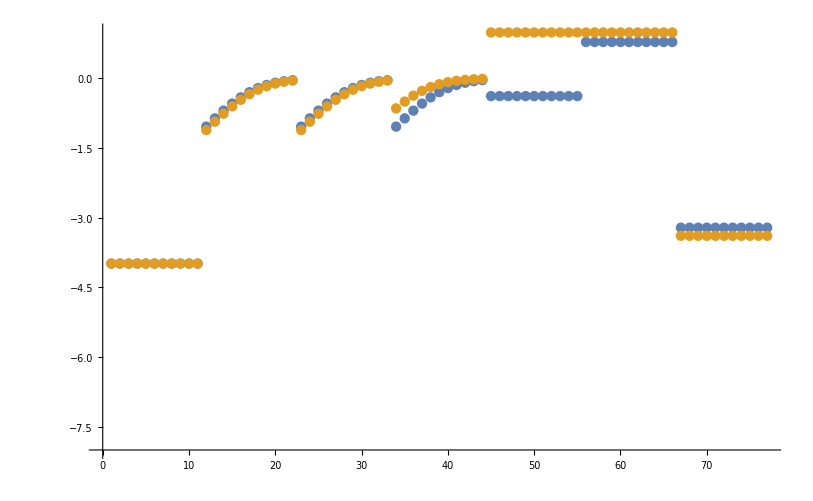

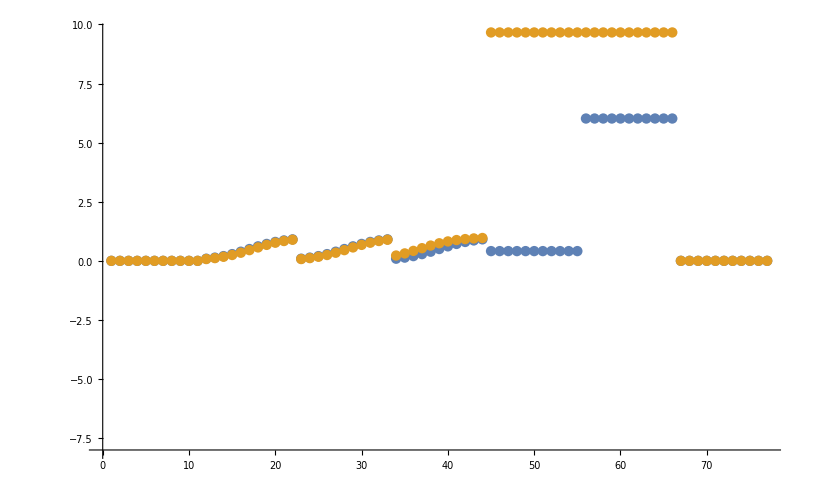

```mathematica
dataSetI=3;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

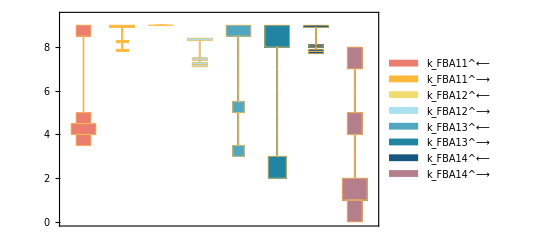

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

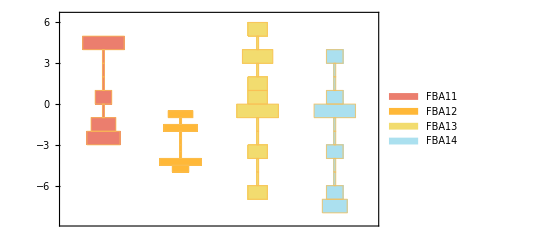

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

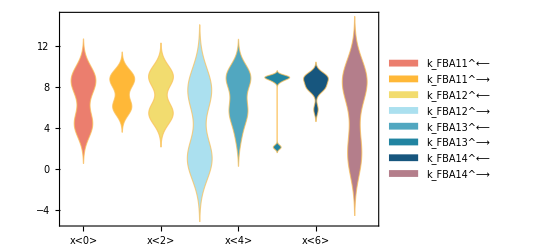

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

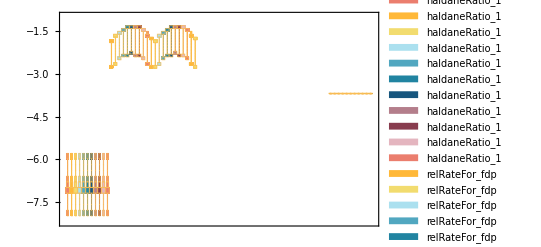

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

4.73405 | 9. | 8.99963 | 7.22066 | 8.90487 | 9. | 7.81217 | 1.24109

#### Parameter Cluster Plots (Optional)

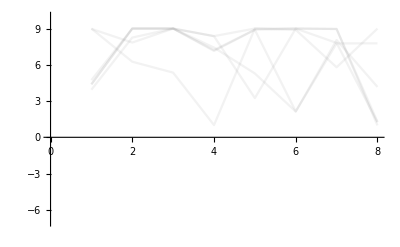

{-Graphics-}

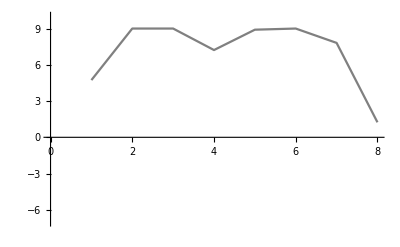

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.00002 | 0.0000242742 | 21.3711
0.00002 | 0.0000242742 | 21.3711
0.00007 | 0.0000242742 | 65.3225

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.412114 | 9.65741 | 2243.38
6.02029 | 9.65741 | 60.4145

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000102656 | 0.00010258 | 0.0739342

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000102656 | 0.00010258 | 0.0739342

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

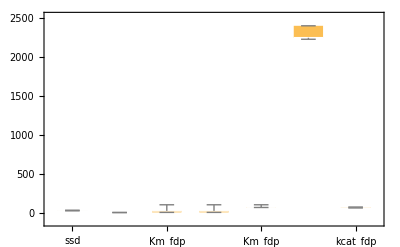

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 5;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/fba1 already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba1\rateconst_labels_fba1.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba1\S_fba1.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_FBA1[c],E_FBA1[c]&dhap,E_FBA1[c]&fdp,dhap[c],fdp[c],g3p[c],E_FBA1[c]&dhap&g3p}

/Users/guest/Desktop/internship stuff/MASSef/examples/fba1\species_fba1.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{FBA11: E_FBA1[c] + fdp[c] <=> E_FBA1[c]&fdp,FBA12: E_FBA1[c]&dhap <=> dhap[c] + E_FBA1[c],FBA13: E_FBA1[c]&fdp <=> E_FBA1[c]&dhap&g3p,FBA14: E_FBA1[c]&dhap&g3p <=> E_FBA1[c]&dhap + g3p[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/fba1\reactions_fba1.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_FBA1[c],E_FBA1[c]&dhap,E_FBA1[c]&fdp,E_FBA1[c]&dhap&g3p}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_FBA11_rev*k_FBA12_fwd*k_FBA13_rev*param_FBA1_total) - k_FBA11_rev*k_FBA12_fwd*k_FBA14_fwd*param_FBA1_total - k_FBA12_fwd*k_FBA13_fwd*k_FBA14_fwd*param_FBA1_total - g3p(c)*k_FBA11_rev*k_FBA13_rev*k_FBA14_rev*param_FBA1_total)/(fdp(c)*k_FBA11_fwd*k_FBA12_fwd*k_FBA13_fwd + fdp(c)*k_FBA11_fwd*k_FBA12_fwd*k_FBA13_rev + k_FBA11_rev*k_FBA12_fwd*k_FBA13_rev + dhap(c)*k_FBA11_rev*k_FBA12_rev*k_FBA13_rev + fdp(c)*k_FBA11_fwd*k_FBA12_fwd*k_FBA14_fwd + k_FBA11_rev*k_FBA12_fwd*k_FBA14_fwd + dhap(c)*k_FBA11_rev*k_FBA12_rev*k_FBA14_fwd + fdp(c)*k_FBA11_fwd*k_FBA13_fwd*k_FBA14_fwd + k_FBA12_fwd*k_FBA13_fwd*k_FBA14_fwd + dhap(c)*k_FBA12_rev*k_FBA13_fwd*k_FBA14_fwd + dhap(c)*g3p(c)*k_FBA11_rev*k_FBA12_rev*k_FBA14_rev + fdp(c)*g3p(c)*k_FBA11_fwd*k_FBA13_fwd*k_FBA14_rev + dhap(c)*g3p(c)*k_FBA12_rev*k_FBA13_fwd*k_FBA14_rev + fdp(c)*g3p(c)*k_FBA11_fwd*k_FBA13_rev*k_FBA14_rev + g3p(c)*k_FBA11_rev*k_FBA13_rev*k_FBA14_rev + dhap(c)*g3p(c)*k_FBA12_rev*k_FBA13_rev*k_FBA14_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba1\rateconst_clusters_fba1.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba1\rateLaw_fba1.txt